The following codes shall only be run once!!!

```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
$LibraryPath=AppendTo[$LibraryPath,FileNameJoin[{NotebookDirectory[],"../MLL-lib"}]];
ClearAll[LegendreRuleMLL,DunavantRuleMLL]
LegendreRuleMLL=LibraryFunctionLoad["lib-franklin","LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRuleMLL=LibraryFunctionLoad["lib-franklin","DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
(*
SetDirectory[FileNameJoin[{NotebookDirectory[],"../ML-exe"}]];
Install["DunavantRule.exe"];
Install["LegendreRule.exe"];
(*Install More Executables Here...*)
ResetDirectory[];
*)
```

## Quadrature Rules and Numerical Integration - Modular

```mathematica
ClearAll[LegendreRule,DunavantRule]
LegendreRule[order_,xmin_,xmax_]:=LegendreRuleMLL[order,xmin,xmax]//Quiet;
DunavantRule[rule_,p_]:=Module[{qx,qy,q,w},
{qx,qy,w}=DunavantRuleMLL[rule,p]//Quiet;
q={qx,qy}ᵀ//ToPackedArray;
w=w//ToPackedArray;
{q,w}
]
ClearAll[QuadratureProduct2D]
QuadratureProduct2D[{q1_, w1_}, {q2_, w2_}] := Module[{q,w},
q=Outer[{#1,#2}&,q1,q2]//Flatten[#,1]&//N//ToPackedArray;
w=Outer[Times,w1,w2]//Flatten[#,1]&//N//ToPackedArray;
{q,w}
]
ClearAll[NIntegrateDuffyTriangle,NIntegrateNonSingularTriangle]
NIntegrateDuffyTriangle[p_,fun_,{q_,w_}]:=
Module[{qq,ww,P0P1,P1P2,P1P2Sq,λ1,λ2,A,b,n,DetA},
P0P1=p⟦2⟧-p⟦1⟧;
P1P2=p⟦3⟧-p⟦2⟧;
A={P0P1,P1P2}//Transpose;
DetA=Abs[Det[A]];
b=p⟦1⟧;
n=Length[q];
P1P2Sq=Total[P1P2^2];
λ1=P0P1.P1P2/P1P2Sq;
λ2=DetA/P1P2Sq;
qq=A.{#⟦1⟧,#⟦1⟧#⟦2⟧}+b&/@q;
ww=Table[w⟦i⟧/Sqrt[(q⟦i,2⟧+λ1)^2+λ2^2],{i,n}];
DetA/Sqrt[P1P2Sq]*∑_(i=1)^n ww⟦i⟧fun[qq⟦i⟧]
]
NIntegrateNonSingularTriangle[p_,fun_,{q_,w_}]:=
Module[{n,A,b,AreaOver2,qq},
n=Length[q];
A={p⟦3⟧-p⟦1⟧,p⟦2⟧-p⟦1⟧}ᵀ;
b=p⟦2⟧+p⟦3⟧;
AreaOver2=0.25*Abs[Det[A]];
qq=0.5*(A.#+b&/@q);
AreaOver2∑_(i=1)^n w⟦i⟧fun[qq⟦i⟧]
]
```

Compute the near singular integral over the triangle:
	(1,0),(0,2),(3,2)

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x;
Print["true value = ",a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-p⟦1⟧],{y,0,2},{x,1-y/2,1+y}]];
Module[{q,w},
Table[
{q,w}=QuadratureProduct2D[LegendreRule[n1,0,1],LegendreRule[n2,0,1]];
Log@Abs[(NIntegrateDuffyTriangle[p,fun,{q,w}]-a0)/a0],
{n1,30},{n2,30}]//ListPlot3D[#,AxesLabel->{"n1","n2","Log(relative error)"},PlotLabel->fun[{x,y}],ImageSize->Large]&//Print
];
```

true value = 3.31753

-Graphics3D-

Compute the non-singular integral over the triangle
	(1,0),(0,2),(3,2)

true value = 273.333

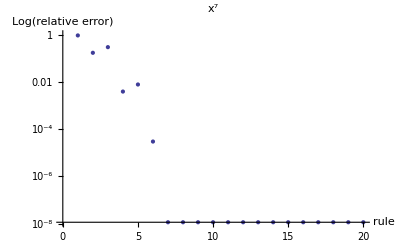

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x^7;
Print["true value = ",a0=NIntegrate[fun[{x,y}],{y,0,2},{x,1-y/2,1+y}]];
Module[{q,w,pStd},
pStd={{-1,-1},{-1,1},{1,-1}};
Table[
{q,w}=DunavantRule[rule,pStd];
Abs[(NIntegrateNonSingularTriangle[p,fun,{q,w}]-a0)/a0],
{rule,1,20}
]//ListLogPlot[#,AxesLabel->{"rule","Log(relative error)"},PlotLabel->fun[{x,y}]]&//Print
];
```

```mathematica
ClearAll[ConstructQuadratureRules,VscnmFunc,VscnmFuncDuffy,VscnmQuadrature]

ConstructQuadratureRules[ruleN_,ruleNp_,{nNpS1_,nNpS2_}]:=
Module[{pStd,qxNpS,qyNpS,wNpS,qNpS},
pStd={{-1,-1},{-1,1},{1,-1}};
{qxNpS,qyNpS,wNpS}=QuadratureProduct2D[LegendreRule[nNpS1,0,1],LegendreRule[nNpS2,0,1]];
qNpS={qxNpS,qyNpS}ᵀ//ToPackedArray;
wNpS=wNpS//ToPackedArray;
{DunavantRule[ruleN,pStd],DunavantRule[ruleNp,pStd],{qNpS,wNpS}}
]
VscnmFunc[m_,r_,rp_]:=Module[{dr,R,Phi},
dr=r-rp;R=Norm[dr];Phi=ArcTan[dr⟦1⟧,dr⟦2⟧];
(*Exp[-ⅈ m Phi]/R*mus[rp]*PhaseFunc[Phi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m Phi]/R*mus[rp]*PhaseFunc[Phi-phis]*Exp[-rp⟦1⟧]
]
VscnmFuncDuffy[m_,r_,rp_]:=With[{Phi=(r-rp)//ArcTan[#⟦1⟧,#⟦2⟧]&},
(*Exp[-ⅈ m Phi]*mus[rp]*PhaseFunc[Phi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m Phi]*mus[rp]*PhaseFunc[Phi-phis]*Exp[-rp⟦1⟧]
]
VscnmQuadrature[n_,m_,{{qN_,wN_},{qNp_,wNp_},{qNpS_,wNpS_}}]:=
Module[{nN,nNp,nNpS,AN,bN,AreaOver2N,qqN,Vscnm,i,r,np,xxN},
nN=Length[qN];
nNp=Length[qNp];
nNpS=Length[qNpS];
AN={pt⟦n,3⟧-pt⟦n,1⟧,pt⟦n,2⟧-pt⟦n,1⟧}ᵀ;
bN=pt⟦n,2⟧+pt⟦n,3⟧;
AreaOver2N=0.25*Abs[Det[AN]];
qqN=0.5*(AN.#+bN&/@qN);
Vscnm=0.0;
For[i=1,i≤nN,i++,
r=qqN⟦i⟧;
xxN=0.0;
For[np=1,np<n,np++,xxN+=NIntegrateNonSingularTriangle[pt⟦np⟧,VscnmFunc[m,r,#]&,{qNp,wNp}];];
For[np=n+1,np≤Ns,np++,xxN+=NIntegrateNonSingularTriangle[pt⟦np⟧,VscnmFunc[m,r,#]&,{qNp,wNp}];];
xxN+=NIntegrateDuffyTriangle[{r,pt⟦n,1⟧,pt⟦n,2⟧},VscnmFuncDuffy[m,r,#]&,{qNpS,wNpS}];
xxN+=NIntegrateDuffyTriangle[{r,pt⟦n,2⟧,pt⟦n,3⟧},VscnmFuncDuffy[m,r,#]&,{qNpS,wNpS}];
xxN+=NIntegrateDuffyTriangle[{r,pt⟦n,3⟧,pt⟦n,1⟧},VscnmFuncDuffy[m,r,#]&,{qNpS,wNpS}];
xxN*=wN⟦i⟧;
Vscnm+=xxN;
];
Vscnm*=AreaOver2N;
Vscnm
]
ClearAll[VscnmQuadratureDebugUse]
VscnmQuadratureDebugUse[n_,m_,ruleN_,ruleNp_,{nNpS1_,nNpS2_}]:=
With[{quadrules=ConstructQuadratureRules[ruleN,ruleNp,{nNpS1,nNpS2}]},VscnmQuadrature[n,m,quadrules]]
```

Outside of pt⟦np⟧: False

r={0.105,0.758632}

cntr⟦np⟧={0.151174,0.758632}

|r-rp|≃0.0461741

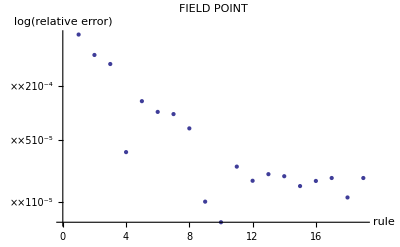

```mathematica
ClearAll[m,np,rule,pStd,point,data]
pStd={{-1,-1},{-1,1},{1,-1}};
rule=5;
m=0;
np=1;
point={0.105,0.758632};
Print["Outside of pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
data=Table[NIntegrateNonSingularTriangle[pt⟦np⟧,VscnmFunc[m,point,#]&,DunavantRule[rule,pStd]],{rule,1,20}];
Abs@(#-data⟦-1⟧&/@data)//ListLogPlot[#,PlotLabel->"FIELD POINT",AxesLabel->{"rule","log(relative error)"}]&
```

```mathematica
ClearAll[i,res,n,m]
{n,m}={30,9};
{nNpS1,nNpS2}={10,10};
res=ConstantArray[0.0,{13,2}];
Print["i=0;Vsc_old(n,m)=",Vsc⟦iGTbl⟦n,m+Nd+1⟧⟧];
For[i=1,i≤13,i++,
res⟦i⟧=VscnmQuadratureDebugUse[n,m,i,i,{nNpS1,nNpS2}]//AbsoluteTiming;
Print["i=",i,";{time,result}=",res⟦i⟧];
]
res⟦All,1⟧//Total;
ave=Total[res⟦All,2⟧]/Length[res];
Abs@(res⟦All,2⟧-ConstantArray[ave,Length[res]])//ListLogPlot//Print;
```

i=0;Vsc_old(n,m)=0.0000586807+0.0000180634 ⅈ

Set::shape: Lists {qxNpS$26853328, qyNpS$26853328, wNpS$26853328} and {{{0.0130467, 0.0130467}, {0.0130467, 0.0674683}, {0.0130467, 0.160295}, {0.0130467, 0.283302}, « 43 », {0.425563, 0.839705}, {0.425563, 0.932532}, {0.425563, 0.986953}, « 50 »}, {0.00111127, « 49 », « 50 »}} are not the same shape.

Transpose::nmtx: The first two levels of the one-dimensional list {qxNpS$26853328, qyNpS$26853328} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {0.760112  - 0.0615957\ qxNpS$26853328 + 0.123082\ qxNpS$26853328\ qyNpS$26853328, 0.716213  - 0.0340963\ qxNpS$26853328 - 0.00362477\ qxNpS$26853328\ qyNpS$26853328} cannot be transposed.

Part::partd: Part specification wNpS$26853328 ⟦ 1 ⟧ is longer than depth of object.

CompiledFunction::cfsa: Argument ArcTan[0.  + 0.0615957\ qxNpS$26853328 - 0.123082\ qxNpS$26853328\ qyNpS$26853328, 0.  + 0.0340963\ qxNpS$26853328 + 0.00362477\ qxNpS$26853328\ qyNpS$26853328] at position 1 should be a "machine-size real number".

Transpose::nmtx: The first two levels of the one-dimensional list {0.760112  + 0.0614862\ qxNpS$26853328 - 0.0613766\ qxNpS$26853328\ qyNpS$26853328, 0.716213  - 0.037721\ qxNpS$26853328 + 0.109538\ qxNpS$26853328\ qyNpS$26853328} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Part::partd: Part specification wNpS$26853328 ⟦ 1 ⟧ is longer than depth of object.

CompiledFunction::cfsa: Argument ArcTan[0.  - 0.0614862\ qxNpS$26853328 + 0.0613766\ qxNpS$26853328\ qyNpS$26853328, 0.  + 0.037721\ qxNpS$26853328 - 0.109538\ qxNpS$26853328\ qyNpS$26853328] at position 1 should be a "machine-size real number".

Part::partd: Part specification wNpS$26853328 ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

CompiledFunction::cfsa: Argument ArcTan[0.  - 0.000109553\ qxNpS$26853328 + 0.0617053\ qxNpS$26853328\ qyNpS$26853328, 0.  - 0.0718173\ qxNpS$26853328 + 0.105914\ qxNpS$26853328\ qyNpS$26853328] at position 1 should be a "machine-size real number".

General::stop: Further output of CompiledFunction :: cfsa will be suppressed during this calculation.

i=1;{time,result}={0.25068,0.00331493 (0.+2. ((0.0046067+0.00271962 ⅈ)+(0.00126714 ⅇ^(-0.760112+0.0615957 qxNpS$26853328-0.123082 qxNpS$26853328 qyNpS$26853328-9 ⅈ ArcTan[0.+0.0615957 qxNpS$26853328-0.123082 qxNpS$26853328 qyNpS$26853328,0.+0.0340963 qxNpS$26853328+0.00362477 qxNpS$26853328 qyNpS$26853328]) wNpS$26853328⟦1⟧)/(√(0.0849759+(-0.49186+qyNpS$26853328)^2) (1.36-(1.2 (0.+0.0615957 qxNpS$26853328-0.123082 qxNpS$26853328 qyNpS$26853328))/(√((0.+0.0615957 qxNpS$26853328-0.123082 qxNpS$26853328 qyNpS$26853328)^2+(0.+0.0340963 qxNpS$26853328+0.00362477 qxNpS$26853328 qyNpS$26853328)^2))))+(0.00124266 ⅇ^(-0.760112-0.0614862 qxNpS$26853328+0.0613766 qxNpS$26853328 qyNpS$26853328-9 ⅈ ArcTan[0.-0.0614862 qxNpS$26853328+0.0613766 qxNpS$26853328 qyNpS$26853328,0.+0.037721 qxNpS$26853328-0.109538 qxNpS$26853328 qyNpS$26853328]) wNpS$26853328⟦1⟧)/(√(0.0785954+(-0.501449+qyNpS$26853328)^2) (1.36-(1.2 (0.-0.0614862 qxNpS$26853328+0.0613766 qxNpS$26853328 qyNpS$26853328))/(√((0.+0.037721 qxNpS$26853328-0.109538 qxNpS$26853328 qyNpS$26853328)^2+(0.-0.0614862 qxNpS$26853328+0.0613766 qxNpS$26853328 qyNpS$26853328)^2))))+(0.00127291 ⅇ^(-0.760112-0.000109553 qxNpS$26853328+0.0617053 qxNpS$26853328 qyNpS$26853328-9 ⅈ ArcTan[0.-0.000109553 qxNpS$26853328+0.0617053 qxNpS$26853328 qyNpS$26853328,0.-0.0718173 qxNpS$26853328+0.105914 qxNpS$26853328 qyNpS$26853328]) wNpS$26853328⟦1⟧)/(√(0.0865334+(-0.506694+qyNpS$26853328)^2) (1.36-(1.2 (0.-0.000109553 qxNpS$26853328+0.0617053 qxNpS$26853328 qyNpS$26853328))/(√((0.-0.000109553 qxNpS$26853328+0.0617053 qxNpS$26853328 qyNpS$26853328)^2+(0.-0.0718173 qxNpS$26853328+0.105914 qxNpS$26853328 qyNpS$26853328)^2))))))}

Set::shape: Lists {qxNpS$26856205, qyNpS$26856205, wNpS$26856205} and {{{0.0130467, 0.0130467}, {0.0130467, 0.0674683}, {0.0130467, 0.160295}, {0.0130467, 0.283302}, « 43 », {0.425563, 0.839705}, {0.425563, 0.932532}, {0.425563, 0.986953}, « 50 »}, {0.00111127, « 49 », « 50 »}} are not the same shape.

i=2;{time,result}={0.09593,0.00331493 (0.+0.666667 ((0.000498625+0.00568042 ⅈ)+(0.000633572 ⅇ^(-0.790855+0.0923388 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.+0.0923388 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205,0.+0.0152358 qxNpS$26856205+0.00362477 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.021244+(-0.74593+qyNpS$26856205)^2) (1.36-(1.2 (0.+0.0923388 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0923388 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205)^2+(0.+0.0152358 qxNpS$26856205+0.00362477 qxNpS$26856205 qyNpS$26856205)^2))))+(0.000621329 ⅇ^(-0.790855-0.0307431 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.-0.0307431 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205,0.+0.0188605 qxNpS$26856205-0.109538 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.0196488+(-0.250725+qyNpS$26856205)^2) (1.36-(1.2 (0.-0.0307431 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0188605 qxNpS$26856205-0.109538 qxNpS$26856205 qyNpS$26856205)^2+(0.-0.0307431 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205)^2))))+(0.00254582 ⅇ^(-0.790855+0.0306335 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.+0.0306335 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205,0.-0.0906778 qxNpS$26856205+0.105914 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.346133+(-0.513387+qyNpS$26856205)^2) (1.36-(1.2 (0.+0.0306335 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0306335 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205)^2+(0.-0.0906778 qxNpS$26856205+0.105914 qxNpS$26856205 qyNpS$26856205)^2)))))+0.666667 ((0.00327533-0.00381197 ⅈ)+(0.000633572 ⅇ^(-0.729314+0.0307979 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.+0.0307979 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205,0.+0.0170481 qxNpS$26856205+0.00362477 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.021244+(-0.24593+qyNpS$26856205)^2) (1.36-(1.2 (0.+0.0307979 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0307979 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205)^2+(0.+0.0170481 qxNpS$26856205+0.00362477 qxNpS$26856205 qyNpS$26856205)^2))))+(0.00248531 ⅇ^(-0.729314-0.0922841 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.-0.0922841 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205,0.+0.0206729 qxNpS$26856205-0.109538 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.314382+(-0.502898+qyNpS$26856205)^2) (1.36-(1.2 (0.-0.0922841 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0206729 qxNpS$26856205-0.109538 qxNpS$26856205 qyNpS$26856205)^2+(0.-0.0922841 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205)^2))))+(0.000636455 ⅇ^(-0.729314-0.0309074 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.-0.0309074 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205,0.-0.0888654 qxNpS$26856205+0.105914 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.0216333+(-0.753347+qyNpS$26856205)^2) (1.36-(1.2 (0.-0.0309074 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205))/(√((0.-0.0309074 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205)^2+(0.-0.0888654 qxNpS$26856205+0.105914 qxNpS$26856205 qyNpS$26856205)^2)))))+0.666667 ((-0.000407325+0.00477556 ⅈ)+(0.00253429 ⅇ^(-0.760166+0.0616505 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.+0.0616505 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205,0.+0.0700049 qxNpS$26856205+0.00362477 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.339904+(-0.48372+qyNpS$26856205)^2) (1.36-(1.2 (0.+0.0616505 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0616505 qxNpS$26856205-0.123082 qxNpS$26856205 qyNpS$26856205)^2+(0.+0.0700049 qxNpS$26856205+0.00362477 qxNpS$26856205 qyNpS$26856205)^2))))+(0.000621329 ⅇ^(-0.760166-0.0614314 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.-0.0614314 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205,0.+0.0736297 qxNpS$26856205-0.109538 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.0196488+(-0.750725+qyNpS$26856205)^2) (1.36-(1.2 (0.-0.0614314 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205))/(√((0.+0.0736297 qxNpS$26856205-0.109538 qxNpS$26856205 qyNpS$26856205)^2+(0.-0.0614314 qxNpS$26856205+0.0613766 qxNpS$26856205 qyNpS$26856205)^2))))+(0.000636455 ⅇ^(-0.760166-0.0000547765 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205-9 ⅈ ArcTan[0.-0.0000547765 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205,0.-0.0359087 qxNpS$26856205+0.105914 qxNpS$26856205 qyNpS$26856205]) wNpS$26856205⟦1⟧)/(√(0.0216333+(-0.253347+qyNpS$26856205)^2) (1.36-(1.2 (0.-0.0000547765 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205))/(√((0.-0.0000547765 qxNpS$26856205+0.0617053 qxNpS$26856205 qyNpS$26856205)^2+(0.-0.0359087 qxNpS$26856205+0.105914 qxNpS$26856205 qyNpS$26856205)^2))))))}

Set::shape: Lists {qxNpS$26858319, qyNpS$26858319, wNpS$26858319} and {{{0.0130467, 0.0130467}, {0.0130467, 0.0674683}, {0.0130467, 0.160295}, {0.0130467, 0.283302}, « 43 », {0.425563, 0.839705}, {0.425563, 0.932532}, {0.425563, 0.986953}, « 50 »}, {0.00111127, « 49 », « 50 »}} are not the same shape.

General::stop: Further output of Set :: shape will be suppressed during this calculation.

i=3;{time,result}={0.15783,0.00331493 (0.+1.04167 ((0.0025948+0.00336111 ⅈ)+(0.000760286 ⅇ^(-0.784706+0.0861902 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.+0.0861902 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319,0.+0.0190079 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0305913+(-0.695116+qyNpS$26858319)^2) (1.36-(1.2 (0.+0.0861902 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0861902 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319)^2+(0.+0.0190079 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319)^2))))+(0.000745594 ⅇ^(-0.784706-0.0368917 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.0368917 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319,0.+0.0226326 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0282943+(-0.300869+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.0368917 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0226326 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0368917 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319)^2))))+(0.00229124 ⅇ^(-0.784706+0.0244849 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.+0.0244849 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319,0.-0.0869057 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.280368+(-0.512049+qyNpS$26858319)^2) (1.36-(1.2 (0.+0.0244849 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0244849 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0869057 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319)^2)))))+1.04167 ((0.00251927-0.0118539 ⅈ)+(0.000760286 ⅇ^(-0.735473+0.0369574 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.+0.0369574 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319,0.+0.0204578 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0305913+(-0.295116+qyNpS$26858319)^2) (1.36-(1.2 (0.+0.0369574 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0369574 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319)^2+(0.+0.0204578 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319)^2))))+(0.00223678 ⅇ^(-0.735473-0.0861245 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.0861245 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319,0.+0.0240825 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.254649+(-0.502608+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.0861245 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0240825 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0861245 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319)^2))))+(0.000763746 ⅇ^(-0.735473-0.0247478 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.0247478 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319,0.-0.0854558 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.031152+(-0.704016+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.0247478 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319))/(√((0.-0.0247478 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0854558 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319)^2)))))-1.125 ((0.000639118+0.00793895 ⅈ)+(0.00126714 ⅇ^(-0.760112+0.0615957 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.+0.0615957 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319,0.+0.0340963 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0849759+(-0.49186+qyNpS$26858319)^2) (1.36-(1.2 (0.+0.0615957 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0615957 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319)^2+(0.+0.0340963 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319)^2))))+(0.00124266 ⅇ^(-0.760112-0.0614862 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.0614862 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319,0.+0.037721 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0785954+(-0.501449+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.0614862 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.037721 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0614862 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319)^2))))+(0.00127291 ⅇ^(-0.760112-0.000109553 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.000109553 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319,0.-0.0718173 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0865334+(-0.506694+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.000109553 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319))/(√((0.-0.000109553 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0718173 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319)^2)))))+1.04167 ((-0.00998195-0.00379245 ⅈ)+(0.00228086 ⅇ^(-0.760156+0.0616396 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.+0.0616396 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319,0.+0.0628232 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.275322+(-0.485348+qyNpS$26858319)^2) (1.36-(1.2 (0.+0.0616396 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.0616396 qxNpS$26858319-0.123082 qxNpS$26858319 qyNpS$26858319)^2+(0.+0.0628232 qxNpS$26858319+0.00362477 qxNpS$26858319 qyNpS$26858319)^2))))+(0.000745594 ⅇ^(-0.760156-0.0614424 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.0614424 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319,0.+0.066448 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.0282943+(-0.700869+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.0614424 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319))/(√((0.+0.066448 qxNpS$26858319-0.109538 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0614424 qxNpS$26858319+0.0613766 qxNpS$26858319 qyNpS$26858319)^2))))+(0.000763746 ⅇ^(-0.760156-0.0000657317 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319-9 ⅈ ArcTan[0.-0.0000657317 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319,0.-0.0430904 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319]) wNpS$26858319⟦1⟧)/(√(0.031152+(-0.304016+qyNpS$26858319)^2) (1.36-(1.2 (0.-0.0000657317 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319))/(√((0.-0.0000657317 qxNpS$26858319+0.0617053 qxNpS$26858319 qyNpS$26858319)^2+(0.-0.0430904 qxNpS$26858319+0.105914 qxNpS$26858319 qyNpS$26858319)^2))))))}

i=4;{time,result}={0.24965,0.00331493 (0.+0.219903 ((-0.0000143353+0.00260689 ⅈ)+(0.000348121 ⅇ^(-0.804706+0.10619 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.10619 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884,0.+0.00673828 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00641363+(-0.860399+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.10619 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.10619 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884)^2+(0.+0.00673828 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884)^2))))+(0.000341393 ⅇ^(-0.804706-0.016892 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.016892 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884,0.+0.0103631 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00593205+(-0.137762+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.016892 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0103631 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.016892 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884)^2))))+(0.00311932 ⅇ^(-0.804706+0.0444846 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0444846 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884,0.-0.0991753 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.519647+(-0.516403+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0444846 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0444846 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0991753 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884)^2)))))+0.219903 ((0.00204866-0.00273147 ⅈ)+(0.000348121 ⅇ^(-0.715438+0.0169221 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0169221 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884,0.+0.00936722 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00641363+(-0.135128+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0169221 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0169221 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884)^2+(0.+0.00936722 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884)^2))))+(0.00304518 ⅇ^(-0.715438-0.10616 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.10616 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884,0.+0.012992 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.471978+(-0.503551+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.10616 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.012992 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.10616 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884)^2))))+(0.000349705 ⅇ^(-0.715438-0.0447832 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.0447832 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884,0.-0.0965464 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00653118+(-0.864475+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.0447832 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884))/(√((0.-0.0447832 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0965464 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884)^2)))))+0.446763 ((-0.000498639+0.00379424 ⅈ)+(0.000410946 ⅇ^(-0.760075+0.0615587 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0615587 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884,0.+0.00983312 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00893746+(-0.49736+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0615587 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0615587 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884)^2+(0.+0.00983312 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884)^2))))+(0.00166248 ⅇ^(-0.760075-0.0615232 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.0615232 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884,0.+0.0134579 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.140672+(-0.333016+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.0615232 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0134579 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0615232 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884)^2))))+(0.00170296 ⅇ^(-0.760075-0.000146565 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.000146565 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884,0.-0.0960805 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.15488+(-0.677878+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.000146565 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884))/(√((0.-0.000146565 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0960805 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884)^2)))))+0.446763 ((0.00108617+0.00624336 ⅈ)+(0.00169524 ⅇ^(-0.780922+0.0824056 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0824056 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884,0.+0.0456155 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.152092+(-0.658033+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0824056 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0824056 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884)^2+(0.+0.0456155 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884)^2))))+(0.000403005 ⅇ^(-0.780922-0.0406763 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.0406763 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884,0.+0.0492403 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00826638+(-0.50047+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.0406763 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0492403 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0406763 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884)^2))))+(0.00170296 ⅇ^(-0.780922+0.0207003 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0207003 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884,0.-0.060298 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.15488+(-0.340032+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0207003 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0207003 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.060298 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884)^2)))))+0.446763 ((0.00230033+0.00277274 ⅈ)+(0.00169524 ⅇ^(-0.739339+0.0408229 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0408229 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884,0.+0.0468402 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.152092+(-0.320187+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0408229 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0408229 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884)^2+(0.+0.0468402 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884)^2))))+(0.00166248 ⅇ^(-0.739339-0.082259 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.082259 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884,0.+0.0504649 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.140672+(-0.670861+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.082259 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0504649 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.082259 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884)^2))))+(0.000412816 ⅇ^(-0.739339-0.0208824 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.0208824 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884,0.-0.0590734 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00910126+(-0.502171+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.0208824 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884))/(√((0.-0.0208824 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0590734 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884)^2)))))+0.219903 ((0.000899719+0.00368219 ⅈ)+(0.00310519 ⅇ^(-0.760191+0.0616752 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.+0.0616752 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884,0.+0.0861833 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.510294+(-0.480053+qyNpS$26861884)^2) (1.36-(1.2 (0.+0.0616752 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0616752 qxNpS$26861884-0.123082 qxNpS$26861884 qyNpS$26861884)^2+(0.+0.0861833 qxNpS$26861884+0.00362477 qxNpS$26861884 qyNpS$26861884)^2))))+(0.000341393 ⅇ^(-0.760191-0.0614067 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.0614067 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884,0.+0.0898081 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00593205+(-0.863034+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.0614067 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884))/(√((0.+0.0898081 qxNpS$26861884-0.109538 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0614067 qxNpS$26861884+0.0613766 qxNpS$26861884 qyNpS$26861884)^2))))+(0.000349705 ⅇ^(-0.760191-0.0000300973 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884-9 ⅈ ArcTan[0.-0.0000300973 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884,0.-0.0197303 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884]) wNpS$26861884⟦1⟧)/(√(0.00653118+(-0.139203+qyNpS$26861884)^2) (1.36-(1.2 (0.-0.0000300973 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884))/(√((0.-0.0000300973 qxNpS$26861884+0.0617053 qxNpS$26861884 qyNpS$26861884)^2+(0.-0.0197303 qxNpS$26861884+0.105914 qxNpS$26861884 qyNpS$26861884)^2))))))}

$Aborted

$Aborted

-Graphics-

## Dumping and Reading .msh File - Modular

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[sprtr,ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
If[$OperatingSystem=="MacOSX",sprtr="_";,0.0];
If[$OperatingSystem=="Windows",sprtr="_";,0.0];
If[$OperatingSystem=="Linux",sprtr="_";,0.0];

ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"mesh"}]
```

/Users/qzmfrank/Codes/rte2dvis/notebook/mesh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

OpenRead::noopen: Cannot open "/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial.msh".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 2}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 3}].

ConstantArray::argt: ConstantArray called with 0 arguments; 2 or 3 arguments are expected.

{False,False}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

OpenRead::noopen: Cannot open "/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26.msh".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 2}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 3}].

ConstantArray::argt: ConstantArray called with 0 arguments; 2 or 3 arguments are expected.

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial_dat/triangles.dat

Import::nffil: File not found during Import.

{False,False}

{Norm[$Failed]+Norm[-ConstantArray[0.,{Read[$Failed,Number],2}]],Norm[$Failed]+Norm[-Floor[ConstantArray[]]]}

## Direct Integral Solver - Sequential, Interpretive and Partially Compiled

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,Phasef,Phasef1,Phasef2,PhaseFunc,PhaseFunc1,phis,Nd]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
mus[{x_,y_}]:=0.5Log[2.0]
mua[{x_,y_}]:=Log[2.0]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.6;
Phasef1[m_]:=g^Abs[m]
Phasef2[m_]:=If[m==0,1.0,0.0]
Phasef=Phasef1;
PhaseFunc1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi])),CompilationTarget:>"C"];
PhaseFunc=PhaseFunc1;
phis=0;
Nd=10;

ClearAll[iG,iL,Rank,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
Rank[x_]:=Length/@{x,xᵀ}//Quiet
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rXYPreCalc,r2rRPreCalc,r2rPhiPreCalc,r2rFPreCalc,AreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
r2rXYPreCalc[cntr_]:=Outer[If[#1<#2,Subtract@@cntr⟦{#1,#2}⟧,{0.0,0.0}]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#-#ᵀ&
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
r2rPhiPreCalc[cntr_]:=Outer[If[#1≠#2,(Subtract@@cntr⟦{#1,#2}⟧//ArcTan[#⟦1⟧,#⟦2⟧]&),0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray
r2rFPreCalc[r2rPhi_,phis_]:=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];
AreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Abs//Divide[#,2.0]&;

ClearAll[Np,p,t,Nn,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area,Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea,musTbl,muaTbl,mutTbl]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nn=Ns;Nm=2Nd+1;Ng=Nn*Nm;
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nn,Nm,Ng}=",{Ns,Nd,Nn,Nm,Ng}];
gTbl=Phasef/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rXY=(r2rXY=r2rXYPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rPhi=(r2rPhi=r2rPhiPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rF=(r2rF=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=AreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}=",{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}//{Total[#],#}&];
Print["{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}=",PackedArrayQ/@{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}];
musTbl=mus/@cntr//ToPackedArray;
muaTbl=mua/@cntr//ToPackedArray;
mutTbl=musTbl+muaTbl;
Print["{musTbl,muaTbl,mutTbl}=",{musTbl,muaTbl,mutTbl}//Map[{PackedArrayQ[#],Rank[#]}&,#]&];


ClearAll[V,VRe,VIm,VElemtRe,VElemtIm,TVRe,TVIm]
VElemtRe=area⟦#⟦1⟧⟧Cos[#⟦2⟧phis]&;
VElemtIm=area⟦#⟦1⟧⟧Sin[#⟦2⟧phis]&;
VElemt=area⟦#⟦1⟧⟧Exp[-ⅈ#⟦2⟧phis]&;
TVRe=(VRe=1.0*VElemtRe[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
TVIm=(VIm=1.0*VElemtIm[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
V=1.0*VRe-1.0ⅈ*VIm;
Print["{TVRe,TVIm}=",{TVRe,TVIm}//{Total[#],#}&];
Print["{V,VRe,VIm}=",PackedArrayQ/@{V,VRe,VIm}];
Print["Norm[V]=",Norm[V]];

ClearAll[Zon1,Zon2,Zoff,vTblC,uTblC,TZon1,TZon2,TZoff,TvTblC,TuTblC]
TZon1=(Zon1=2π area+2 π^(1/2)mutTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZon2=(Zon2=-2 π^(1/2)musTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZoff=(Zoff=Outer[If[#2>#1,area⟦#1⟧area⟦#2⟧/r2rR⟦#1,#2⟧,0.0]&,Range[Ns],Range[Ns]]//ToPackedArray//#+#ᵀ&;)//AbsoluteTiming//#⟦1⟧&;

TvTblC=(vTblC=Compile[{{r2rPhi,_Real,2},{Ns,_Integer},{Nd,_Integer}},
Table[Exp[-ⅈ r2rPhi⟦n,np⟧Range[-Nd,Nd]],{n,Ns},{np,Ns}],
Parallelization->True
,CompilationTarget:>"C"
][r2rPhi,Ns,Nd];)//AbsoluteTiming//#⟦1⟧&;
TuTblC=(uTblC=Compile[{{musTbl,_Real,1},{mutTbl,_Real,1},{gTbl,_Real,1},{vTblC,_Complex,3},{r2rPhi,_Real,2},{Ns,_Integer}},
Table[mutTbl⟦np⟧vTblC⟦n,np⟧*-musTbl⟦np⟧gTbl vTblC⟦n,np⟧*,{n,Ns},{np,Ns}],
Parallelization->True
,CompilationTarget:>"C"
][musTbl,mutTbl,gTbl,vTblC,r2rPhi,Ns];
)//AbsoluteTiming//#⟦1⟧&;

Print["{TZon1,TZon2,TZoff,TvTblC,TuTblC}=",{TZon1,TZon2,TZoff,TvTblC,TuTblC}//{Total[#],#}&];
Print["{Zon1,Zon2,Zoff,vTblC,uTblC}=",PackedArrayQ/@{Zon1,Zon2,Zoff,vTblC,uTblC}];

ClearAll[ZDotXC0,ZDotXC,ZDotXCcounter]
ZDotXCcounter=0;
ZDotXC0=Compile[{{X,_Complex,1},{Ns,_Integer},{Nd,_Integer},{gTbl,_Real,1},{Zon1,_Real,1},{Zon2,_Real,1},{Zoff,_Real,2},{vTblC,_Complex,3},{uTblC,_Complex,3}},
  Module[{Xp,Yp,temp,n,np},
    Xp=Partition[X,2Nd+1];
    Flatten@Table[
      temp=ConstantArray[0.0+0.0I,2Nd+1];
      For[np=1,np<=Ns,np++,
        If[np==n,
          temp+=Zon1[[n]]Xp[[n]]+Zon2[[n]]gTbl Xp[[n]];,
          temp+=Zoff[[n,np]](Xp[[np]].uTblC[[n,np]])vTblC[[n,np]];
        ];  
      ];  
      temp
      ,{n,Ns}]
  ],  
  Parallelization->True
  ,CompilationTarget:>"C"
][#,Ns,Nd,gTbl,Zon1,Zon2,Zoff,vTblC,uTblC]&;
ZDotXC[V_]:=Module[{},ZDotXCcounter++;ZDotXC0[V]]
Print["ZDotXC[V] time=",ZDotXC[V]//AbsoluteTiming//#[[1]]&];


ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
,CompilationTarget:>"C"
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];

ClearAll[damp,Tdamp1,damp1]
Tdamp1=(damp1=Exp[-mutTbl⟦1⟧cntr⟦All,1⟧];)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp1=",Tdamp1];
Print["damp1=",damp1//PackedArrayQ];

ClearAll[OpticalPathC,damp2C,Tdamp2C]
OpticalPathC=Compile[{{P0,_Real,1},{phi,_Real},{mutTbl,_Real,1},{pt,_Real,3},{Ns,_Integer}},
Module[{np,tau=0.0},For[np=1,np≤Ns,np++,tau+=mutTbl⟦np⟧*HalfLineTriangleSegmentC[phi,P0,pt⟦np⟧];];tau]
(*,CompilationTarget:>"C"*)
][#1,#2,mutTbl,pt,Ns]&;

Tdamp2C=(damp2C=Exp[Table[-OpticalPathC[cntr⟦n⟧,phis+π],{n,Ns}]]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp2C=",Tdamp2C]
Print["damp2C=",damp2C//PackedArrayQ];
Print["Norm[damp2C-damp1]=",Norm[damp2C-damp1]]

damp=damp2C;
ClearAll[Von,Voff,Vsc,TVsc]
TVsc=(
Von=musTbl √(area/π)damp;
Voff=((Zoff r2rF)ᵀ(damp musTbl))ᵀ;
Vsc=Von(Partition[V,Nm]ᵀg)ᵀ;
For[n=1,n≤Ns,n++,
For[np=1,np≤Ns,np++,
Vsc⟦n⟧+=Voff⟦n,np⟧vTblC⟦n,np⟧;
];
];
Vsc=Flatten[Vsc];)//AbsoluteTiming//#⟦1⟧&;
Print["Vsc=",PackedArrayQ[Vsc]];
Print["TVsc=",TVsc];
ClearAll[sol2sc,Tsol2sc,sol2scp]
Tsol2sc=(sol2sc=LinearSolve[ZDotXC[#]&,Vsc,Method->{"Krylov",Tolerance->Norm[Vsc]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2sc=",Tsol2sc];
Print["Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=",Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]];
Print["Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=",Max[Norm/@(ZDotXC[sol2sc]-Vsc)]/Norm[Vsc]];
sol2scp=Partition[sol2sc,Nm];
Print["sym sol2sc=",Table[Norm[sol2scp⟦n⟧-sol2scp⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];
Print["Nd residual=",(sol2scp⟦All,1⟧//Map[Norm,#]&//Norm)/(sol2scp⟦All,Nd+1⟧//Map[Norm,#]&//Norm)];
```

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/triangles.dat

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nn,Nm,Ng}={162,10,162,21,3402}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}={0.3318,{0.00018,0.00014,0.0669,0.07908,0.14218,0.04277,0.00053}}

{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}={True,True,True,True,True,True,True}

{musTbl,muaTbl,mutTbl}={{True,{162,1}},{True,{162,1}},{True,{162,1}}}

{TVRe,TVIm}={0.02495,{0.01265,0.0123}}

{V,VRe,VIm}={True,True,True}

Norm[V]=0.364955

{TZon1,TZon2,TZoff,TvTblC,TuTblC}={0.3875,{0.00004,0.00002,0.06225,0.17926,0.14595}}

{Zon1,Zon2,Zoff,vTblC,uTblC}={True,True,True,True,True}

ZDotXC[V] time=0.1865

Tdamp1=0.00002

damp1=True

Tdamp2C=0.26363

damp2C=True

Norm[damp2C-damp1]=5.32444×10^-16

Vsc=True

TVsc=0.18563

Tsol2sc=3.56293

Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=6.62615×10^-10

Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=9.2645×10^-11

sym sol2sc=0.126915

Nd residual=0.113137

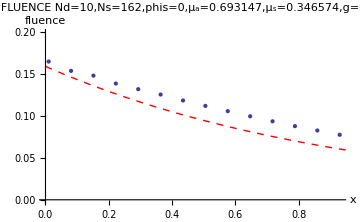

```mathematica
ClearAll[A,y,CoordTbl,nTbl,data,n,pltstr,fluence]
sol2scp=Partition[sol2sc,Nm];
y=0.5;A=Total[area];
CoordTbl=Table[{x,y},{x,0.01,0.99,0.9 √(A/N[Ns])}];
nTbl=PickTriangle/@CoordTbl;
data=Transpose@{CoordTbl⟦All,1⟧,sol2scp⟦nTbl,Nd+1⟧//Re};
For[n=1,n≤Length[data],n++,data⟦n,2⟧+=Exp[-OpticalPathC[CoordTbl⟦n⟧,phis+π]]/(2π);];
pltstr="NEW FLUENCE\n"<>"Nd="<>ToString[Nd]<>",Ns="<>ToString[Ns]<>",phis="<>ToString[phis]<>",μ_a="<>ToString[mua[{0,0}]]<>",μ_s="<>ToString[mus[{0,0}]]<>",g="<>ToString[g]<>",y="<>ToString[y];
Print@Show[
ListPlot[data,PlotRange->{0,1/(2π)+0.04},PlotLabel->pltstr,AxesLabel->{"x","fluence"},PlotStyle->{PointSize[Medium]},ImageSize->Medium],
Plot[Exp[-mut[{0.,0.}]x]/(2π),{x,0,1},PlotStyle->{Red,Dashed,Thick}]
]
fluence=Interpolation[{cntr,sol2scp⟦All,Nd+1⟧32}//Chop//Transpose]//Quiet;
DensityPlot[fluence[x,y]+Exp[-mutTbl⟦1⟧x]/(2π),{x,0,1},{y,0,1},AspectRatio->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->Medium,AxesLabel->{"x","y"}]//Quiet;
```